```mathematica
data1 = Import["/net/home/f09/bajennissen/research/DAY196/tau_day_data/368nm.dat"]
data1hour=Drop[data1, None,1]
data2 = Import["/net/home/f09/bajennissen/research/DAY196/tau_day_data/412nm.dat"]
data2hour=Drop[data2,None,1]
data3 = Import["/net/home/f09/bajennissen/research/DAY196/tau_day_data/500nm.dat"]
data3hour=Drop[data3,None,1]
data4 = Import["/net/home/f09/bajennissen/research/DAY196/tau_day_data/610nm.dat"]
data4hour=Drop[data4,None,1]
data5 = Import["/net/home/f09/bajennissen/research/DAY196/tau_day_data/675nm.dat"]
data5hour=Drop[data5,None,1]
data6= Import["/net/home/f09/bajennissen/research/DAY196/tau_day_data/778nm.dat"]
data6hour=Drop[data6,None,1]
data7 = Import["/net/home/f09/bajennissen/research/DAY196/tau_day_data/862nm.dat"]
data7hour=Drop[data7,None,1]
```

{{196.326,7.81667,0.114378},{196.333,7.98333,0.119118},{196.34,8.15,0.134454},{196.347,8.31667,0.148103},{196.354,8.5,0.119493},{196.36,8.65,0.124926},{196.367,8.81667,0.151749},{196.374,8.98333,0.239554},{196.382,9.16667,0.233198},{196.392,9.4,0.252905},{196.401,9.61667,0.421935},{196.408,9.8,0.683266},{196.417,10,0.939749},{196.424,10.1667,1.26386},{196.431,10.35,1.65857},{196.438,10.5,1.85441},{196.451,10.8167,0.898572},{196.458,11,0.915266},{196.465,11.15,0.935395},{196.472,11.3333,1.094},{196.478,11.4833,1.17517},{196.485,11.65,1.29748},{196.492,11.8167,1.40165}}

{{7.81667,0.114378},{7.98333,0.119118},{8.15,0.134454},{8.31667,0.148103},{8.5,0.119493},{8.65,0.124926},{8.81667,0.151749},{8.98333,0.239554},{9.16667,0.233198},{9.4,0.252905},{9.61667,0.421935},{9.8,0.683266},{10,0.939749},{10.1667,1.26386},{10.35,1.65857},{10.5,1.85441},{10.8167,0.898572},{11,0.915266},{11.15,0.935395},{11.3333,1.094},{11.4833,1.17517},{11.65,1.29748},{11.8167,1.40165}}

{{196.326,7.81667,0.118138},{196.333,7.98333,0.127983},{196.34,8.15,0.142943},{196.347,8.31667,0.158218},{196.354,8.5,0.132417},{196.36,8.65,0.142152},{196.367,8.81667,0.164102},{196.374,8.98333,0.242959},{196.382,9.16667,0.253762},{196.392,9.4,0.273637},{196.401,9.61667,0.390741},{196.408,9.8,0.525883},{196.417,10,0.630325},{196.424,10.1667,0.772945},{196.431,10.35,0.878096},{196.438,10.5,0.925835},{196.451,10.8167,0.629493},{196.458,11,0.661465},{196.465,11.15,0.670879},{196.472,11.3333,0.749667},{196.478,11.4833,0.806722},{196.485,11.65,0.824326},{196.492,11.8167,0.93503}}

{{7.81667,0.118138},{7.98333,0.127983},{8.15,0.142943},{8.31667,0.158218},{8.5,0.132417},{8.65,0.142152},{8.81667,0.164102},{8.98333,0.242959},{9.16667,0.253762},{9.4,0.273637},{9.61667,0.390741},{9.8,0.525883},{10,0.630325},{10.1667,0.772945},{10.35,0.878096},{10.5,0.925835},{10.8167,0.629493},{11,0.661465},{11.15,0.670879},{11.3333,0.749667},{11.4833,0.806722},{11.65,0.824326},{11.8167,0.93503}}

{{196.326,7.81667,0.0966198},{196.333,7.98333,0.103547},{196.34,8.15,0.116249},{196.347,8.31667,0.123961},{196.354,8.5,0.11125},{196.36,8.65,0.116049},{196.367,8.81667,0.132197},{196.374,8.98333,0.196334},{196.382,9.16667,0.207714},{196.392,9.4,0.218691},{196.401,9.61667,0.281426},{196.408,9.8,0.342143},{196.417,10,0.38061},{196.424,10.1667,0.444203},{196.431,10.35,0.477214},{196.438,10.5,0.494227},{196.451,10.8167,0.376672},{196.458,11,0.413364},{196.465,11.15,0.416555},{196.472,11.3333,0.458462},{196.478,11.4833,0.480832},{196.485,11.65,0.486644},{196.492,11.8167,0.552206}}

{{7.81667,0.0966198},{7.98333,0.103547},{8.15,0.116249},{8.31667,0.123961},{8.5,0.11125},{8.65,0.116049},{8.81667,0.132197},{8.98333,0.196334},{9.16667,0.207714},{9.4,0.218691},{9.61667,0.281426},{9.8,0.342143},{10,0.38061},{10.1667,0.444203},{10.35,0.477214},{10.5,0.494227},{10.8167,0.376672},{11,0.413364},{11.15,0.416555},{11.3333,0.458462},{11.4833,0.480832},{11.65,0.486644},{11.8167,0.552206}}

{{196.326,7.81667,0.113863},{196.333,7.98333,0.118363},{196.34,8.15,0.125769},{196.347,8.31667,0.133462},{196.354,8.5,0.12432},{196.36,8.65,0.127469},{196.367,8.81667,0.13846},{196.374,8.98333,0.18597},{196.382,9.16667,0.191179},{196.392,9.4,0.197906},{196.401,9.61667,0.256601},{196.408,9.8,0.308534},{196.417,10,0.352452},{196.424,10.1667,0.402613},{196.431,10.35,0.439396},{196.438,10.5,0.457254},{196.451,10.8167,0.351669},{196.458,11,0.37154},{196.465,11.15,0.378849},{196.472,11.3333,0.410134},{196.478,11.4833,0.428937},{196.485,11.65,0.428866},{196.492,11.8167,0.479832}}

{{7.81667,0.113863},{7.98333,0.118363},{8.15,0.125769},{8.31667,0.133462},{8.5,0.12432},{8.65,0.127469},{8.81667,0.13846},{8.98333,0.18597},{9.16667,0.191179},{9.4,0.197906},{9.61667,0.256601},{9.8,0.308534},{10,0.352452},{10.1667,0.402613},{10.35,0.439396},{10.5,0.457254},{10.8167,0.351669},{11,0.37154},{11.15,0.378849},{11.3333,0.410134},{11.4833,0.428937},{11.65,0.428866},{11.8167,0.479832}}

{{196.326,7.81667,0.0849385},{196.333,7.98333,0.0895333},{196.34,8.15,0.0995219},{196.347,8.31667,0.103718},{196.354,8.5,0.0975956},{196.36,8.65,0.101578},{196.367,8.81667,0.11564},{196.374,8.98333,0.15147},{196.382,9.16667,0.157256},{196.392,9.4,0.168521},{196.401,9.61667,0.227375},{196.408,9.8,0.302575},{196.417,10,0.356107},{196.424,10.1667,0.427241},{196.431,10.35,0.481413},{196.438,10.5,0.505247},{196.451,10.8167,0.369564},{196.458,11,0.374604},{196.465,11.15,0.389027},{196.472,11.3333,0.425799},{196.478,11.4833,0.438037},{196.485,11.65,0.452977},{196.492,11.8167,0.505363}}

{{7.81667,0.0849385},{7.98333,0.0895333},{8.15,0.0995219},{8.31667,0.103718},{8.5,0.0975956},{8.65,0.101578},{8.81667,0.11564},{8.98333,0.15147},{9.16667,0.157256},{9.4,0.168521},{9.61667,0.227375},{9.8,0.302575},{10,0.356107},{10.1667,0.427241},{10.35,0.481413},{10.5,0.505247},{10.8167,0.369564},{11,0.374604},{11.15,0.389027},{11.3333,0.425799},{11.4833,0.438037},{11.65,0.452977},{11.8167,0.505363}}

{{196.326,7.81667,0.107215},{196.333,7.98333,0.103965},{196.34,8.15,0.112096},{196.347,8.31667,0.122715},{196.354,8.5,0.115625},{196.36,8.65,0.119038},{196.367,8.81667,0.141599},{196.374,8.98333,0.158423},{196.382,9.16667,0.170072},{196.392,9.4,0.178157},{196.401,9.61667,0.274705},{196.408,9.8,0.441254},{196.417,10,0.596714},{196.424,10.1667,0.730976},{196.431,10.35,0.89274},{196.438,10.5,0.981236},{196.451,10.8167,0.607046},{196.458,11,0.603466},{196.465,11.15,0.605484},{196.472,11.3333,0.668651},{196.478,11.4833,0.71116},{196.485,11.65,0.749912},{196.492,11.8167,0.785338}}

{{7.81667,0.107215},{7.98333,0.103965},{8.15,0.112096},{8.31667,0.122715},{8.5,0.115625},{8.65,0.119038},{8.81667,0.141599},{8.98333,0.158423},{9.16667,0.170072},{9.4,0.178157},{9.61667,0.274705},{9.8,0.441254},{10,0.596714},{10.1667,0.730976},{10.35,0.89274},{10.5,0.981236},{10.8167,0.607046},{11,0.603466},{11.15,0.605484},{11.3333,0.668651},{11.4833,0.71116},{11.65,0.749912},{11.8167,0.785338}}

{{196.326,7.81667,0.0796361},{196.333,7.98333,0.0789926},{196.34,8.15,0.0936598},{196.347,8.31667,0.0930097},{196.354,8.5,0.0860145},{196.36,8.65,0.0932946},{196.367,8.81667,0.108724},{196.374,8.98333,0.124144},{196.382,9.16667,0.137583},{196.392,9.4,0.152267},{196.401,9.61667,0.3229},{196.408,9.8,0.693886},{196.417,10,1.13533},{196.424,10.1667,1.67826},{196.431,10.35,3.66164},{196.438,10.5,inf},{196.451,10.8167,1.17707},{196.458,11,1.01604},{196.465,11.15,1.16635},{196.472,11.3333,1.28949},{196.478,11.4833,1.46164},{196.485,11.65,1.57262},{196.492,11.8167,1.70356}}

{{7.81667,0.0796361},{7.98333,0.0789926},{8.15,0.0936598},{8.31667,0.0930097},{8.5,0.0860145},{8.65,0.0932946},{8.81667,0.108724},{8.98333,0.124144},{9.16667,0.137583},{9.4,0.152267},{9.61667,0.3229},{9.8,0.693886},{10,1.13533},{10.1667,1.67826},{10.35,3.66164},{10.5,inf},{10.8167,1.17707},{11,1.01604},{11.15,1.16635},{11.3333,1.28949},{11.4833,1.46164},{11.65,1.57262},{11.8167,1.70356}}

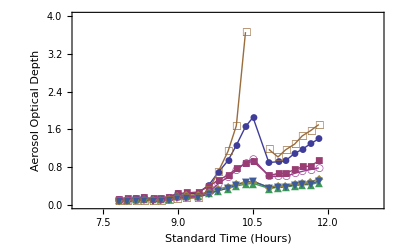

```mathematica
<<PlotLegends`
DataPlot=ListPlot[{data1hour,data2hour,data3hour,data4hour,data5hour,data6hour,data7hour}, PlotStyle->PointSize[0.02],PlotMarkers->Automatic,Joined->True,PlotLegend->{"368nm","412nm","500nm","610nm","675nm","778nm","862nm"},LegendPosition->{1.1,-0.4}, LegendSize->{0.5,0.75},PlotRange->{{7,13},{0,4}},Frame->True, AxesOrigin-> {7,0},LegendShadow->None,FrameLabel->{{"Aerosol Optical Depth",""},{"Standard Time (Hours)","Day 196 July 15th, 2010"}}]
```